### The equation

The historical version of the Blausius Equation (the one with the 1/2 without redefining f and η with 1/sqrt(2) in them) is...
   f ’’’ + f f ’’ / 2 = 0

which has boundary conditions...
  f (0) = 0
  f ‘ (0) = 0
  f ‘ (∞) = 1

### Creating a non-linear system (which MATLAB can directly solve)

First step is to convert to a system of 1st-order ODE’s using
   f1 = f
   f2 = f’
   f3 = f2’ = f ’’
So we get the system...
   f1‘ = f2
   f2’ = f3
   f3’ = - f1 * f3 / 2

This can easily be solved in MATLAB...

      guess = 0.332; % initial f3 value
      finalEta = 10; % should be large when modifying the above value
 
      f = @(t,x) [x(2);x(3);-x(1)*x(3)/2];
      [eta,sol] = ode45(f,[0,finalEta],[0,0,guess]);
      
      plot(eta,sol(:,1))
      xlabel(‘eta’), ylabel(‘f’)
 
      sol(end,2) % check final f’ value (should be 1)

### Linearizing the system to complete the Keller Box Method

However, we need to linearize the 3rd equation to solve this in the Keller Box Method asked of us. First, we use central differences (with step size h in the variable eta, and j gives the eta)...

```mathematica
(Subscript[f, 1]^(j+1)-Subscript[f, 1]^j)/h = (Subscript[f, 2]^(j+1)+Subscript[f, 2]^j)/2 
(Subscript[f, 2]^(j+1)-Subscript[f, 2]^j)/h = (Subscript[f, 3]^(j+1)+Subscript[f, 3]^j)/2 
(Subscript[f, 3]^(j+1)-Subscript[f, 3]^j)/h = -(Subscript[f, 1]^(j+1)+Subscript[f, 1]^j)*(Subscript[f, 3]^(j+1)+Subscript[f, 3]^j)/8
```

We can linearize this system by doing {f1, f2, f3} -> {f1 + df1, f2 + df2, f3 + df3} and ignoring the higher order terms. This accomplishes an iteration that will get us closer to the final answer from an initial guess (or the previous iteration) by an amount {df1, df2, df3}. We will creat a matrix to solve for the {df1, df2, df3}. The previous iteration will be used to calculate the {f1, f2, f3} values.

```mathematica
(Subscript[df, 1]^(j+1)-Subscript[df, 1]^j)/h - (Subscript[df, 2]^(j+1)+Subscript[df, 2]^j)/2 =-(Subscript[f, 1]^(j+1)-Subscript[f, 1]^j)/h +(Subscript[f, 2]^(j+1)+Subscript[f, 2]^j)/2 
(Subscript[df, 2]^(j+1)-Subscript[df, 2]^j)/h - (Subscript[df, 3]^(j+1)+Subscript[df, 3]^j)/2 =-(Subscript[f, 2]^(j+1)-Subscript[f, 2]^j)/h + (Subscript[f, 3]^(j+1)+Subscript[f, 3]^j)/2 
(Subscript[df, 3]^(j+1)-Subscript[df, 3]^j)/h  +(Subscript[df, 1]^(j+1)*Subscript[f, 3]^(j+1)+Subscript[df, 1]^(j+1)*Subscript[f, 3]^j+Subscript[df, 1]^j*Subscript[f, 3]^(j+1)+Subscript[df, 1]^j*Subscript[f, 3]^j+Subscript[f, 1]^(j+1)*Subscript[df, 3]^(j+1)+Subscript[f, 1]^(j+1)*Subscript[df, 3]^j+Subscript[f, 1]^j*Subscript[df, 3]^(j+1)+Subscript[f, 1]^j*Subscript[df, 3]^j)/8=-(Subscript[f, 3]^(j+1)-Subscript[f, 3]^j)/h  -(Subscript[f, 1]^(j+1)+Subscript[f, 1]^j)*(Subscript[f, 3]^(j+1)+Subscript[f, 3]^j)/8
```

Using f^(j+1/2) = (f^(j+1) + f^j) / 2 as notation for the centered value, this simplifies to...

```mathematica
(Subscript[df, 1]^(j+1)-Subscript[df, 1]^j)/h  +(-Subscript[df, 2]^(j+1)-Subscript[df, 2]^j)/2 =-(Subscript[f, 1]^(j+1)-Subscript[f, 1]^j)/h +Subscript[f, 2]^(j+1/2)
(Subscript[df, 2]^(j+1)-Subscript[df, 2]^j)/h + (-Subscript[df, 3]^(j+1)-Subscript[df, 3]^j)/2 =-(Subscript[f, 2]^(j+1)-Subscript[f, 2]^j)/h + Subscript[f, 3]^(j+1/2) 
(Subscript[df, 3]^(j+1)-Subscript[df, 3]^j)/h  +(Subscript[f, 3]^(j+1/2)Subscript[df, 1]^(j+1)+Subscript[f, 3]^(j+1/2)Subscript[df, 1]^j+Subscript[f, 1]^(j+1/2)*Subscript[df, 3]^(j+1)+Subscript[f, 1]^(j+1/2)*Subscript[df, 3]^j)/4=-(Subscript[f, 3]^(j+1)-Subscript[f, 3]^j)/h  -Subscript[f, 1]^(j+1/2) *Subscript[f, 3]^(j+1/2) /2
```

We have 6 unknowns per equation: df1(j), df2(j), df3(j), df1(j+1), df2(j+1), df3(j+1)
We have j = 1, 2, ...., J-1 sets of equations.
The total system has 3*(J-1) equations and 3*J unknowns:
      df1(1), df2(1), df3(1), df1(2), df2(2), df3(2), ..., df1(J), df2(J), df3(J)
We get the three extra equations from our boundary conditions...
      df1(1) = 0
      df2(1) = 0
      df2(J) = 0

### Look at initial guesses

These have to obey the boundary conditions. For example, the second plot ( f2 = f ‘ ) has f2(0) = 0 and f2(∞) = 1. We got correct results without these initial guesses being consistent (for example, slope of f1 at 0 is not 0).

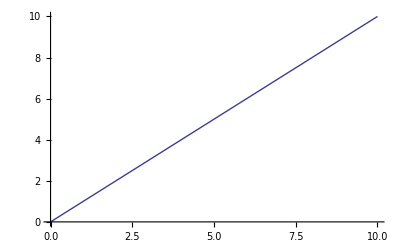

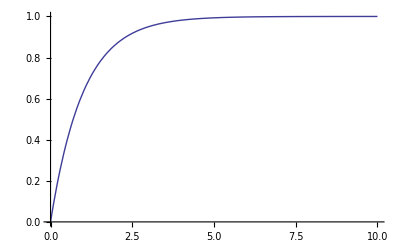

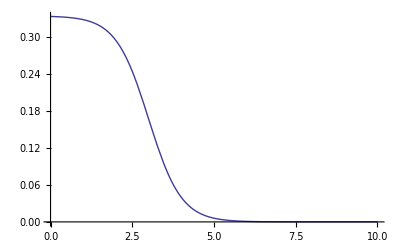

```mathematica
Plot[x,{x,0,10}]
Plot[1-Exp[-x],{x,0,10},PlotRange->All]
Plot[(1-Tanh[x-3])/6,{x,0,10},PlotRange->All]
```